# Stereographic projection

```mathematica
n={0,0,2R};
q={x,y,0};
l=q+λ(n-q);
d=l-{0,0,R};
sol=Simplify[Solve[Dot[d,d]==R^2,λ]];
p=Simplify[l/.sol][[2]];
Print["Parametrization p = ",p];
px=Simplify[D[p,x]];
py=Simplify[D[p,y]];
cE=Simplify[Dot[px,px]];
cF=Simplify[Dot[px,py]];
cG=Simplify[Dot[py,py]];
g={{cE,cF},{cF,cG}};
Print["Metric Tensor = ",MatrixForm[g]]
μc=Simplify[Sqrt[Det[g]],R>0 && x∈Reals && y∈Reals];
Print["Volume form = ", μc];

(* Plotting coordinate functions *)
q=Simplify[({x,y,z}+λ({x,y,z}-n))/.Solve[2r+λ(z-2R)==0,λ]][[1]];
sz=15;
RVal=5;
sG=ParametricPlot3D[p/.R->RVal,{x,-sz,sz},{y,-sz,sz},PlotRange->All,PlotStyle->
Directive[Orange,Opacity[1]],PlotPoints->100,Mesh->20,Boxed->False,Axes->False];
s2G=ContourPlot3D[x^2+y^2+(z-RVal)^2==RVal^2,{x,-RVal,RVal},{y,-RVal,RVal},{z,0,2RVal},Mesh->None,
ContourStyle->Directive[Opacity[.3],Specularity[1]] ];
pG=ParametricPlot3D[{x,y,0},{x,-sz,sz},{y,-sz,sz},Mesh->20,PlotStyle->Directive[Opacity[1]]];
Show[sG,s2G,pG]
```

Parametrization p = {(4 R^2 x)/(4 R^2+x^2+y^2),(4 R^2 y)/(4 R^2+x^2+y^2),(2 R (x^2+y^2))/(4 R^2+x^2+y^2)}

Metric Tensor = ((16 R^4)/((4 R^2+x^2+y^2)^2) | 0
0 | (16 R^4)/((4 R^2+x^2+y^2)^2))

Volume form = (16 R^4)/((4 R^2+x^2+y^2)^2)

-Graphics3D-

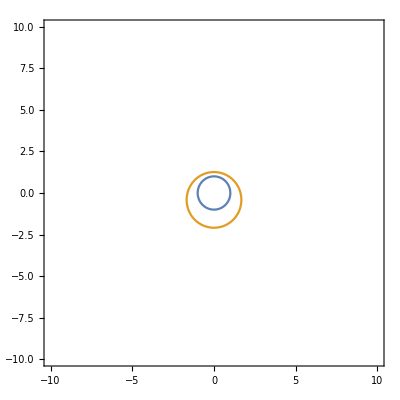

-Graphics3D-

```mathematica
rVal=1;
n1={0,0,1};
n2={0,1,4};
n1=n1/Norm[n1];
n2=n2/Norm[n2];
d1=-.6;
d2=-.2;
spG=ContourPlot3D[x^2+y^2 +(z-rVal)^2==.995rVal,{x,-rVal,rVal},{y,-rVal,rVal},{z,0,2rVal},
ContourStyle->Directive[Orange,Opacity[.5]],
MeshFunctions->{Function[{x,y,z},Dot[{x,y,z-1},n1]],Function[{x,y,z},Dot[{x,y,z-1},n2]]},
MeshStyle->{Directive[Thickness[.005],Opacity[0],Green], Directive[Thickness[.005],Green,Opacity[0]]},
Mesh->{{d1},{d2}},Boxed->False,Axes->False];
sz=10;
eq1=Dot[n1,p-{0,0,rVal}]/.R->rVal;
eq2=Dot[n2,p-{0,0,rVal}]/.R->rVal;
ContourPlot[{eq1==d1,eq2==d2},{x,-sz,sz},{y,-sz,sz},PlotPoints->50]
ch=ImplicitRegion[eq1>=d1 && eq2≤d2,{{x,-sz,sz},{y,-sz,sz}}];
pe=p/.R->rVal;
chG=ParametricPlot3D[pe,{x,y}∈ch,PlotStyle->Directive[Blue]];
ch2G=ParametricPlot3D[{x,y,0.001},{x,y}∈ch,PlotStyle->Directive[Blue]];
Show[spG, chG,ch2G,pG,PlotRange->{{-sz,sz},{-sz,sz},{-sz,sz}}]
(*Region[ch]*)
```

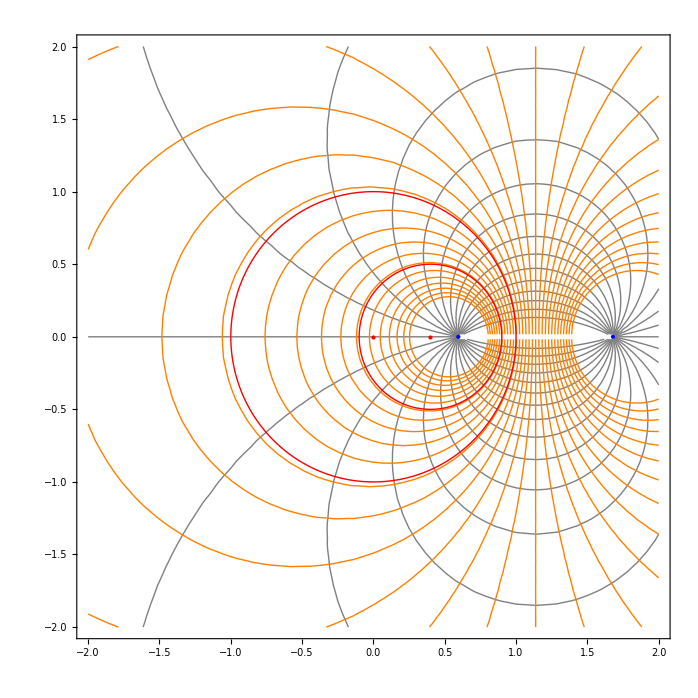

```mathematica
mJ[r1_,r2_,d_]:=Module[{q,c1,myI,out},
q=mq[r1,r2,d];
myI=mI[r1,r2,d];
c1=Sqrt[mq[r1,r2,d]^2+r1^2];
out=-1;
If[(myI==1) && (d<Re[c1]),out=1];
If[(myI==I) && (d<r1+r2),out=1];
out
];
circle[c_,r_]:=c+r(Cos[θ]+I Sin[θ]);
circleG[c_,r_]:={ParametricPlot[{Re[circle[c,r]],Im[circle[c,r]]},{θ,0,2Pi},PlotStyle->{Red,Thick}],Graphics[{PointSize[Large],Red,Point[{Re[c],Im[c]}]}]};
mI[r1_,r2_,d_]:=If[(d^2-(r1+r2)^2)(d^2-(r1-r2)^2)<0,1,I];
mq[r1_,r2_,d_]:=(1/(2d))Sqrt[(d^2-(r1+r2)^2)(d^2-(r1-r2)^2)];
c1c2[r1_,r2_,d_]:={Sqrt[mq[r1,r2,d]^2+r1^2],mJ[r1,r2,d]Sqrt[mq[r1,r2,d]^2+r2^2]};

mP[r1_,r2_,f1_,f2_]:=Module[{q,q1,q2,d,c1,c2},
d=Norm[f2-f1];
{c1,c2}=c1c2[r1,r2,d];
q=mq[r1,r2,d];
q1=(f1 c2 -f2 c1  +q(f2-f1))/(c2-c1);
q2=(f1 c2 -f2 c1  -q(f2-f1))/(c2-c1);
{q1,q2,mI[r1,r2,d] Log[(z-q2)/(z-q1)]}
];
steinerGV2[r1_,r2_,f1_,f2_,range_]:=Module[{q1,q2,P,Pxy,reG,imG,qsG,q,d},
{q1,q2,P}=mP[r1,r2,f1,f2];
Pxy=P/.z->(x+I y );
reG=ContourPlot[Re[Pxy],{x,-range,range},{y,-range,range},ContourShading->None,Contours->30,ContourStyle->Gray];
imG=ContourPlot[Im[Pxy],{x,-range,range},{y,-range,range},ContourShading->None,Contours->30,ContourStyle->Orange];
qsG=Graphics[{PointSize[Large],Blue,Point[{{Re[q1],Im[q1]},{Re[q2],Im[q2]}}]}];
{reG,imG,qsG}
];

(* Example *)
f1val=0;
f2val=.4;
r1val=1;
r2val=.5;
range = 2;
(*Show[Join[steinerG0[r1val,r2val,dval,range],circleG[c1,r1val],circleG[c2,r2val]]]*)
Show[Join[steinerGV2[r1val,r2val,f1val,f2val,range],circleG[f1val,r1val],circleG[f2val,r2val]]]
```